## numerical values of physical constants

#### with units

```mathematica
Ry=13.606*10^-3 keV;
Be=Ry;
a0=5.2918*10^-9 cm;
hbarc=197.33*10^-10 keV cm;
hbar=6.5821*10^-19 keV s;
c=2.9979*10^10 cm/s;
csh=299.79  cm/sh;
mpc2=938.27*10^3 keV;
nnc2=939.6 MeV;
mec2=511. keV;
amuc2=931.19*10^3 keV;
α=1/(137.03599976);

mpkg=1.6726*10^-27 kg;
mnkg=1.6749*10^-27 kg;
mpg=1.6726*10^-24 g;
mng=1.6749*10^-24 g;


NA=6.022*10^23/g (*moles per gram *);
NAkg=6.022*10^26/kg (*moles per gram *);
kBeV=8.618*10^-5 eV/K;
kBJ = 1.3806*10^23 J/K;
Rgas=8.3145 J/( mole*K);
```

#### without units

```mathematica
Ry=13.606*10^-3 ;(* keV *)
Be=Ry;
a0=5.2918*10^-9 ;(* cm *)
hbarc=197.33*10^-10 ;(* keV cm *)
hbar=6.5821*10^-19 ;(* keV s *)
c=2.9979*10^10 ;(* cm/s *)
mpc2=938.27*10^3;(* keV *)
mec2=511. ;(* keV *)
amuc2=931.19*10^3;(* keV *)
α=1/(137.03599976);
```

### unit conversion factors

```mathematica
(* energy conversions *)

J2eV=(1 eV)/(1.602176487 *10^-19 J); ev2j=1/j2ev;
eV2MeV=(1MeV)/(10^6 eV); MeV2eV=1/ eV2MeV;
ev2keV=(1keV)/(10^3 eV);keV2ev=1/ev2keV;
eV2GeV=(1MeV)/(10^9 eV); GeV2eV=1/ eV2GeV;
MeV2t=t/(2.6125*10^22 MeV);  tTOMeV=1/MeV2t;
MeV2kt=kt/(2.6125*10^25 MeV);kt2MeV=1/MeV2kt;
J2jerk=jerk/(10^9 J);  jerk2J=1/J2jerk;

(*distance conversions *)
cm2m =(1m)/(100 cm) ;  m2cm=1/cm2m;
cm2mm=(10mm)/cm;mm2cm=1/cm2mm;
cm2μm = (10^4 μm)/cm; μm2cm = 1/cm2μm;
m2μm = m2cm*cm2μm; μm2m=1/m2μm;
```

### parameter definitions

```mathematica
(* [T]=keV; [n]=cm^-3; [mc2]=keV : the following have been double checked *)
nxTg[T_,g_]:=g^2/(4 π a0^3) (T/(2 Be))^3
λth[T_] := hbarc( (2 π)/(mec2 T))^(1/2)
zSmall[T_,n_] := 1/2 n*λth[T]^3
nxTzSmall[T_,z_]:= (2 z)/λth[T]^3
F[z_]:=4/(√π)NIntegrate[x^2/(Exp[x^2]/z+1),{x,0,∞}]
dF[z_]:=1/z^2 4/(√π)NIntegrate[(x^2 Exp[x^2])/((Exp[x^2]/z+1)^2),{x,0,∞}]
nDegen[T_,z_]:=  2/λth[T]^3 F[z]
zDegen[T_,n_]:=FindRoot[n==1, {n,2.3}]
κ2Degen[T_,z_]:=(2 Be)/T  (2*4π a0)/λth[T]^3 z dF[z] (* not sure if correct *)
```

```mathematica
(* [T]=keV; [n]=cm^-3; [mc2]=keV : the following have been double checked *)
g[T_,n_]:=((2 Be)/T)^(3/2)(4 Pi n a0^3)^(1/2)     (* plasma coupling *)
κ[T_,n_]:=((2 Be)/T)^(1/2)(4 Pi n a0^3)^(1/2)   a0^-1    (* [cm^-1] Debye wave number *)
ω[mc2_,n_] :=(Be/mc2)^(1/2)(8π n a0)^(1/2)*c         (* [s^-1] plasma frequency *)

Vab[mac2_,Ta_,mbc2_,Tb_] :=c √(Ta/mac2 + Tb/mbc2)  (* [cm/s]thermal velocity for temp equil *)
etaab[mac2_,Ta_,Za_, mbc2_,Tb_,Zb_] := (2 Be Abs[Za*Zb] a0 c)/(hbarc*Vab[mac2,Ta,mbc2,Tb])
```

```mathematica
Te=100 keV;
Ti=100 keV; Tp=Ti;
ne=10^25 cm^-3;
Ze=1;
Zp=1;
```

```mathematica
κe=κ[Te,ne]
```

1.3452×10^7 √(1/cm^3) √(1/keV)

```mathematica
Vab[mec2,Te,mpc2,Tp]
```

1.32655×10^10 √keV

```mathematica
g[Te,ne]
```

0.0000193709 √(1/cm^3) (1/keV)^(3/2)

```mathematica
ω[mec2,ne]
```

1.78399×10^17 √(1/cm^3)

```mathematica
etaab[mec2,Te,Ze, mpc2,Tp,Zp]
```

0.0164916/(√keV)

```mathematica
g0=0.1;
z0=0.2;
Plot[{nxTg[T,g0],nDegen[T,z0]},{T,0,0.3}]
```

-Graphics-

```mathematica
g0=0.1;
z0=1;
Plot[{κ[T,nxTz[T,z0]],κDegen[T,z0]},{T,0,1}]
```

Plot::exclul: {Im[1/T] - 0, Im[nxTz[T, 1]] - 0} must be a list of equalities or real-valued functions.

-Graphics-

### old parameter definitions [to do: check consistence]

#### numerical values of physical constants

2.18813×10^-9 √(1/Te)

```mathematica
ZE= 1/2 ne*LAMBDAE^3
```

5.23827×10^-27 ne (1/Te)^(3/2)

```mathematica
ETAE=a0 (2 Be)/hbarc(mec2/Te)^(1/2)/. {cm -> 1, keV -> 1}
```

0.164961 √(1/Te)

```mathematica
OMEGAE=((2 Be)/mec2)^(1/2)(4 π ne a0^3)^(1/2) (c/a0)/. {cm -> 1, keV -> 1} 
KAPPAE*Sqrt[Te/mec2]*c    /. {cm -> 1, keV -> 1, Te -> 1}
```

(56414.9 √ne)/s

(56414.9 √ne)/s

```mathematica
OMEGAP=(Be/mpc2)^(1/2)(8 π ne a0^3)^(1/2) (c/a0)/. {cm -> 1, keV -> 1, ne -> nI}
OMEGAE*Sqrt[mec2/mpc2]/. { ne -> nI}
```

(1316.56 √nI)/s

(1316.56 √nI)/s

```mathematica
LOGBPS=1/2 Log[8 Exp[-EulerGamma-1]* (Te/hbarc)^2 *mec2/(4 π ne) *1/(2 a0)*1/Be ] /. {cm -> 1, keV -> 1}
```

1/2 Log[(1.19833×10^27 Te^2)/ne]

```mathematica
RATEBPS=(8 √(2 π))/3  (4 nI a0^3)/(mec2 mpc2) c/a0 Be^2 (mec2/T)^(3/2)/. {cm -> 1, keV -> 1} 
2/(3 ne)KAPPAE^2/(2 Pi)*OMEGAP^2/c*(mec2/(2Pi Te))^(1/2)/. {cm -> 1, keV -> 1}
TAU=2/(3 ne)1/(2π)Be/Te Be/mpc2(mec2/(2π Te))^(1/2)(8π ne a0^3)(8π nI a0^3)c/a0^4/. {cm -> 1, keV -> 1}
```

(1.00112×10^-13 nI (1/T)^(3/2))/s

(1.00112×10^-13 nI (1/Te)^(3/2))/s

(1.00112×10^-13 nI (1/Te)^(3/2))/s

```mathematica
CeI=1/(2π)Be/Te Be/mpc2(mec2/(2π Te))^(1/2)(8π ne a0^3)(8π nI a0^3)c/a0^4/. {cm -> 1, keV -> 1}
```

(1.50168×10^-13 ne nI (1/Te)^(3/2))/s

```mathematica
LOWELL=1/a0^3 c/a0(8 π)/(√(2π))(ne a0^3)(nI a0^3)mec2/mpc2(2 Be)^2/(√mec2 Te^(3/2))/. {cm -> 1, keV -> 1}
```

(1.50168×10^-13 ne nI)/(s Te^(3/2))

```mathematica
LOGBPSCL=-(1/2)Log[((2 Be)/Te)^3 ((π ne a0^3)/4) Exp[4 EulerGamma+1]]/.{cm->1,keV->1}
```

-1/2 Log[(6.41508×10^-29 ne)/Te^3]

#### numerical expressions for plasma parameters

n   is the number density in 1/cc
T   is the temperature in keV

```mathematica
Clear[n,T,ne,Te,nI,g,kappa,lambdae,ze,etae,omegae,omegap,logBPS,tau,CeI]
gold[n_,T_]:=6.12563*10^-15*Sqrt[n/T^3]                                   (* g coefficient *)
kappaold[n_,T_]:=4.2539*10^-5Sqrt[n/T]                                       (* Debye wave number [1/cm] *)
lambdaeold[Te_]:=2.18813*10^-9 /Sqrt[Te]                                      (* electron thermal wave length [cm] *)
zeold[ne_,Te_] := 5.23827*10^-27*ne/Te^(3/2)                        (* electron fugacity *)
etaeold[Te_] := 0.164961/Sqrt[Te]                                                             (* quantum parameter  *)
omegaeold[ne_] :=5.64149 *10^5 Sqrt[ne]                                              (* 1/s  *)
omegapold[np_] := 1.31650 *10^4 Sqrt[np]                                             (* 1/s *)

 (* BPS Coulomb log in extreme quantum limit *) (* only for hydrogen *)
logBPSold[ne_,Te_]:= 0.5*Log[1.198*10^27 (Te^2/ne)]    
tauold[ne_,nI_,Te_] := 1.001*10^-13 (nI/Te^1.5)  * logBPS[ne,Te]                 (* 1/s *)
CeIold[ne_,nI_,Te_]:= 1.50168*10^-13 (ne nI/Te^1.5)  * logBPS[ne,Te]        (* keV/s-cm^3 *)

(* BPS Coulomb log in extreme quantum limit *) (* only for hydrogen *)
logBPSclold[ne_,Te_]:= 0.5*Log[1.55883*10^28 (Te^3/ne)]    
tauclold[ne_,nI_,Te_] := 1.001*10^-13 (nI/Te^1.5)  * logBPScl[ne,Te]                 (* 1/s *)
CeIclold[ne_,nI_,Te_]:= 1.50168*10^-13 (ne nI/Te^1.5)  * logBPScl[ne,Te]        (* keV/s-cm^3 *)
```

## Plots of A-coefficients (and asymptotics) [check this]

### Acoeff [from acoeff.f90]

```mathematica
st=OpenRead["main.acoeff.dat"];
Do[Read[st,String],{i,1,19}];
ne=Read[st,Number]
Te=Read[st,Number]
Ti=Read[st,Number]
nn=Read[st,Number]
Read[st,String] ;
Read[st,String] ;
dataA=Table[Read[st,{Number,Number,Number,Number,
Number,Number,Number,Number,Number,Number,
Number}],{i,1,nn}];
Close[st];
```

1.×10^25

10.

10.

1601

```mathematica
dataAtot=Table[{dataA[[i,2]],dataA[[i,3]]},{i,1,nn}];
grAtot=ListPlot[dataAtot,Joined-> True];
```

```mathematica
dataAi=Table[{dataA[[i,2]],dataA[[i,4]]},{i,1,nn}];
grAi=ListPlot[dataAi,Joined-> True];
```

```mathematica
dataAe=Table[{dataA[[i,2]],dataA[[i,5]]},{i,1,nn}];
grAe=ListPlot[dataAe,Joined-> True];
```

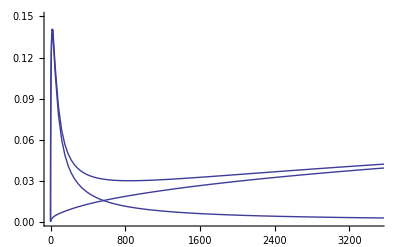

```mathematica
ymax=0.15;
ymin=0;
xmax=3500;
xmin=0;
Show[grAtot,grAi,grAe,PlotRange->{{xmin,xmax},{ymin,ymax}}]
```

```mathematica
dataActot=Table[{dataA[[i,2]],dataA[[i,6]]},{i,1,nn}];
grActot=ListPlot[dataActot,Joined-> True];
```

```mathematica
dataAci=Table[{dataA[[i,2]],dataA[[i,7]]},{i,1,nn}];
grAci=ListPlot[dataAci,Joined-> True];
```

```mathematica
dataAce=Table[{dataA[[i,2]],dataA[[i,8]]},{i,1,nn}];
grAce=ListPlot[dataAce,Joined-> True];
```

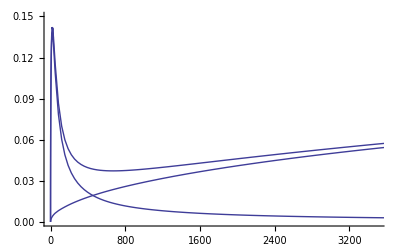

```mathematica
Show[grActot,grAci,grAce,PlotRange->{{xmin,xmax},{ymin,ymax}}]
```

```mathematica
dataAqtot=Table[{dataA[[i,2]],dataA[[i,9]]},{i,1,nn}];
grAqtot=ListPlot[dataAqtot,Joined-> True];
```

```mathematica
dataAqi=Table[{dataA[[i,2]],dataA[[i,10]]},{i,1,nn}];
grAqi=ListPlot[dataAqi,Joined-> True];
```

```mathematica
dataAqe=Table[{dataA[[i,2]],dataA[[i,11]]},{i,1,nn}];
grAqe=ListPlot[dataAqe,Joined-> True];
```

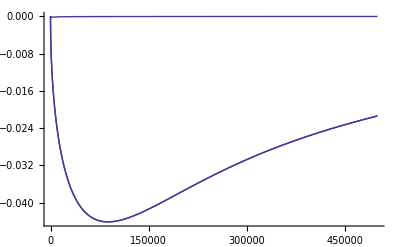

```mathematica
Show[grAqtot,grAqi,grAqe]
```

### Acoeff - small E

```mathematica
st=OpenRead["main.acoeff.smallE.dat"];
Do[Read[st,String],{i,1,19}];
ne=Read[st,Number]
Te=Read[st,Number]
Ti=Read[st,Number]
nn=Read[st,Number]
Read[st,String] ;
Read[st,String] ;
dataSmallE=Table[Read[st,{Number,Number,Number,Number,
Number,Number,Number,Number,Number,Number,Number}],{i,1,nn}];
Close[st];
```

1.×10^25

10.

10.

1601

```mathematica
dataSmallEAtot=Table[{dataSmallE[[i,2]],dataSmallE[[i,3]]},{i,1,nn}];
grSmallEAtot=ListPlot[dataSmallEAtot,Joined-> True];
```

```mathematica
dataSmallEAi=Table[{dataSmallE[[i,2]],dataSmallE[[i,4]]},{i,1,nn}];
grSmallEAi=ListPlot[dataSmallEAi,Joined-> True];
```

```mathematica
dataSmallEAe=Table[{dataSmallE[[i,2]],dataSmallE[[i,5]]},{i,1,nn}];
grSmallEAe=ListPlot[dataSmallEAe,Joined-> True];
```

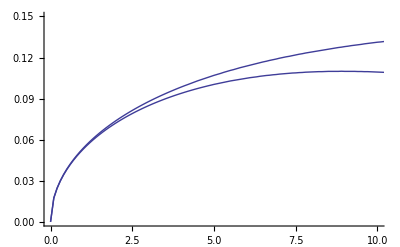

```mathematica
ymax=0.15;
ymin=0;
xmax=10;
xmin=0;
Show[grActot,grSmallEAtot,PlotRange->{{xmin,xmax},{ymin,ymax}}]
```

```mathematica
dataSmallEActot=Table[{dataSmallE[[i,2]],dataSmallE[[i,6]]},{i,1,nn}];
grSmallEActot=ListPlot[dataSmallEActot,Joined-> True];
```

```mathematica
dataSmallEAci=Table[{dataSmallE[[i,2]],dataSmallE[[i,7]]},{i,1,nn}];
grSmallEAci=ListPlot[dataSmallEAci,Joined-> True];
```

```mathematica
dataSmallEAce=Table[{dataSmallE[[i,2]],dataSmallE[[i,8]]},{i,1,nn}];
grSmallEAce=ListPlot[dataSmallEAce,Joined-> True];
```

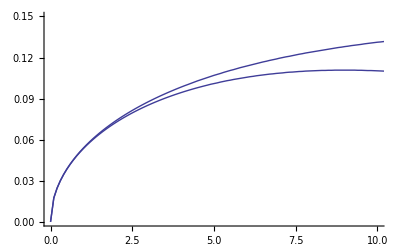

```mathematica
ymax=0.15;
ymin=0;
xmax=10;
xmin=0;
Show[grActot,grSmallEActot,PlotRange->{{xmin,xmax},{ymin,ymax}}]
```

```mathematica
dataSmallEAqtot=Table[{dataSmallE[[i,2]],dataSmallE[[i,9]]},{i,1,nn}];
grSmallEAqtot=ListPlot[dataSmallEAqtot,Joined-> True];
```

```mathematica
dataSmallEAqi=Table[{dataSmallE[[i,2]],dataSmallE[[i,10]]},{i,1,nn}];
grSmallEAqi=ListPlot[dataSmallEAqi,Joined-> True];
```

```mathematica
dataSmallEAqe=Table[{dataSmallE[[i,2]],dataSmallE[[i,11]]},{i,1,nn}];
grSmallEAqe=ListPlot[dataSmallEAqe,Joined-> True];
```

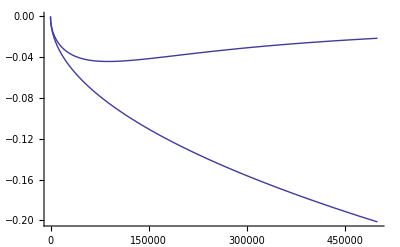

```mathematica
ymax=-0.004;
ymin=0;
xmax=100;
xmin=0;
Show[grAqtot,grSmallEAqtot,PlotRange->{{xmin,xmax},{ymin,ymax}}]
```

### Acoeff - large E

```mathematica
st=OpenRead["main.acoeff.highE.dat"];
Do[Read[st,String],{i,1,19}];
ne=Read[st,Number]
Te=Read[st,Number]
Ti=Read[st,Number]
nn=Read[st,Number]
Read[st,String] ;
Read[st,String] ;
datahighE=Table[Read[st,{Number,Number,Number,Number,
Number,Number,Number,Number,Number,Number,Number}],{i,1,nn}];
Close[st];
```

1.×10^25

10.

10.

1601

```mathematica
datahighEAtot=Table[{datahighE[[i,2]],datahighE[[i,3]]},{i,1,nn}];
grhighEAtot=ListPlot[datahighEAtot,Joined-> True]
```

```mathematica
datahighEAi=Table[{datahighE[[i,2]],datahighE[[i,4]]},{i,1,nn}];
grhighEAi=ListPlot[datahighEAi,Joined-> True]
```

```mathematica
datahighEAe=Table[{datahighE[[i,2]],datahighE[[i,5]]},{i,1,nn}];
grhighEAe=ListPlot[datahighEAe,Joined-> True]
```

```mathematica
ymax=0.15;
ymin=0;
xmax=10;
xmin=0;
Show[grActot,grhighEAtot,PlotRange->{{xmin,xmax},{ymin,ymax}}]
```

```mathematica
datahighEActot=Table[{datahighE[[i,2]],datahighE[[i,6]]},{i,1,nn}];
grhighEActot=ListPlot[datahighEActot,Joined-> True];
```

```mathematica
datahighEAci=Table[{datahighE[[i,2]],datahighE[[i,7]]},{i,1,nn}];
grhighEAci=ListPlot[datahighEAci,Joined-> True];
```

```mathematica
datahighEAce=Table[{datahighE[[i,2]],datahighE[[i,8]]},{i,1,nn}];
grhighEAce=ListPlot[datahighEAce,Joined-> True];
```

```mathematica
ymax=0.15;
ymin=0;
xmax=10;
xmin=0;
Show[grActot,grhighEActot,PlotRange->{{xmin,xmax},{ymin,ymax}}]
```

```mathematica
datahighEAqtot=Table[{datahighE[[i,2]],datahighE[[i,9]]},{i,1,nn}];
grhighEAqtot=ListPlot[datahighEAqtot,Joined-> True];
```

```mathematica
datahighEAqi=Table[{datahighE[[i,2]],datahighE[[i,10]]},{i,1,nn}];
grhighEAqi=ListPlot[datahighEAqi,Joined-> True];
```

```mathematica
datahighEAqe=Table[{datahighE[[i,2]],datahighE[[i,11]]},{i,1,nn}];
grhighEAqe=ListPlot[datahighEAqe,Joined-> True];
```

```mathematica
ymax=-0.004;
ymin=0;
xmax=100;
xmin=0;
Show[grAqtot,grhighEAqtot,PlotRange->{{xmin,xmax},{ymin,ymax}}]
```

## Plots of dE/dx

### dE/dx [from dedx.f90]

```mathematica
st=OpenRead["main.dedx.dat"];
Do[Read[st,String],{i,1,19}];
ne=Read[st,Number]
Te=Read[st,Number]
Ti=Read[st,Number]
nn=Read[st,Number]
Read[st,String];
Read[st,String];
dataA=Table[Read[st,{Number,Number,Number,Number,
Number,Number,Number,Number,Number,Number,
Number}],{i,1,nn}];
Close[st];
```

1.×10^25

10.

10.

1001

```mathematica
ymax=0.05;
ymin=-0.02;
dataAtot=Table[{dataA[[i,2]],dataA[[i,3]]},{i,1,nn}];
grAtot=ListPlot[dataAtot,Joined-> True,PlotRange-> {ymin,ymax}];
```

```mathematica
dataAi=Table[{dataA[[i,2]],dataA[[i,4]]},{i,1,nn}];
grAi=ListPlot[dataAi,Joined-> True];
```

```mathematica
dataAe=Table[{dataA[[i,2]],dataA[[i,5]]},{i,1,nn}];
grAe=ListPlot[dataAe,Joined-> True];
```

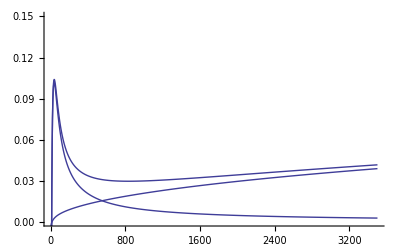

```mathematica
ymax=0.15;
ymin=0;
xmax=3500;
xmin=0;
gr1=Show[grAtot,grAi,grAe,PlotRange->{{xmin,xmax},{ymin,ymax}}]
```

### dE/dx from the A-coefficients

```mathematica
st=OpenRead["main.dedx.fr.acoeff.dat"];
Do[Read[st,String],{i,1,19}];
ne=Read[st,Number]
Te=Read[st,Number]
Ti=Read[st,Number]
nn=Read[st,Number]
Read[st,String];
Read[st,String];
dataA=Table[Read[st,{Number,Number,Number,Number,
Number,Number,Number,Number,Number,Number,
Number}],{i,1,nn}];
Close[st];
```

1.×10^25

10.

10.

1001

```mathematica
ymax=0.05;
ymin=-0.02;
dataAtot=Table[{dataA[[i,2]],dataA[[i,3]]},{i,1,nn}];
grAtot=ListPlot[dataAtot,Joined-> True,PlotRange-> {ymin,ymax}];
```

```mathematica
dataAi=Table[{dataA[[i,2]],dataA[[i,4]]},{i,1,nn}];
grAi=ListPlot[dataAi,Joined-> True];
```

```mathematica
dataAe=Table[{dataA[[i,2]],dataA[[i,5]]},{i,1,nn}];
grAe=ListPlot[dataAe,Joined-> True];
```

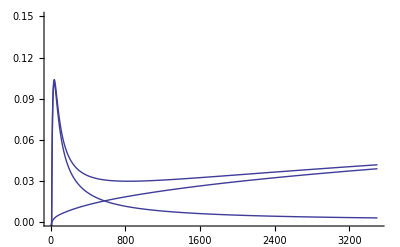

```mathematica
ymax=0.15;
ymin=0;
xmax=3500;
xmin=0;
gr2=Show[grAtot,grAi,grAe,PlotRange->{{xmin,xmax},{ymin,ymax}}]
```

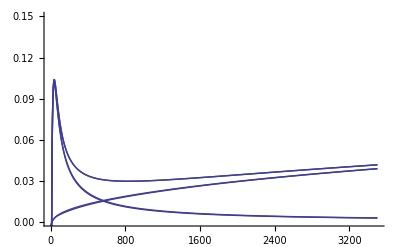

```mathematica
Show[gr1,gr2]
```

## Plots C_ab

### dE/dx [from dedx.f90]

```mathematica
st=OpenRead["main.symmetry.dat"];
Do[Read[st,String],{i,1,10}]
nn=500;
dataA=Table[Read[st,{Number,Number,Number}],{i,1,nn}]
Close[st];
data1=Table[{dataA[[i,2]],dataA[[i,3]]},{i,1,Length[dataA]}];
```

{{1,0.59995,0.00033835206515659284},{3,1.59985,0.00038509273288658076},{5,2.59975,0.00040413630919234066},{7,3.59965,0.00041500931161537243},{9,4.59955,0.00041991597800795005},{11,5.59945,0.0004221920428591058},{13,6.59935,0.00042322750562909039},{15,7.59925,0.00042357051360786225},{17,8.59915,0.00042349560371576805},{19,9.59905,0.00042314357531395675},{21,10.599,0.00042256714252519553},{23,11.5989,0.00042176734898026415},{25,12.5988,0.00042072866965399316},{27,13.5987,0.00041944293562614602},{29,14.5986,0.00041791771951643348},{31,15.5985,0.00041617383552832869},{33,16.5984,0.00041423906424285718},{35,17.5983,0.00041214259293982663},{37,18.5982,0.00040991170044043574},{39,19.5981,0.00040757011411048105},{41,20.598,0.00040513777977673458},{43,21.5979,0.00040263112013073346},{45,22.5978,0.0004000635467349462},{47,23.5977,0.00039744600593024471},{49,24.5976,0.00039478747177792024},{51,25.5975,0.00039209535766915657},{53,26.5974,0.00038937584584240194},{55,27.5973,0.00038663414506243717},{57,28.5972,0.00038387468963218592},{59,29.5971,0.00038110129228896003},{61,30.597,0.00037831726164566491},{63,31.5969,0.00037552549271627542},{65,32.5968,0.00037272853714040189},{67,33.5967,0.00036992865812819371},{69,34.5966,0.0003671278738903523},{71,35.5965,0.00036432799235620828},{73,36.5963,0.00036153063925972289},{75,37.5962,0.0003587372811358946},{77,38.5961,0.00035594924437391232},{79,39.596,0.00035316773118230507},{81,40.5959,0.0003503938331078311},{83,41.5958,0.00034762854259361462},{85,42.5957,0.00034487276294662658},{87,43.5956,0.00034212731699971593},{89,44.5955,0.00033939295469058043},{91,45.5954,0.00033667035973276394},{93,46.5953,0.00033396015551813093},{95,47.5952,0.00033126291036361297},{97,48.5951,0.00032857914219401292},{99,49.595,0.00032590932273653941},{101,50.5949,0.00032325388129012022},{103,51.5948,0.00032061320812250201},{105,52.5947,0.00031798765753998941},{107,53.5946,0.00031537755066802077},{109,54.5945,0.00031278317797557673},{111,55.5944,0.00031020480157172633},{113,56.5943,0.00030764265729895762},{115,57.5942,0.00030509695664490341},{117,58.5941,0.00030256788849107862},{119,59.594,0.00030005562071550376},{121,60.5939,0.0002975603016633925},{123,61.5938,0.0002950820614991112},{125,62.5937,0.00029262101345077735},{127,63.5936,0.00029017725495752316},{129,64.5935,0.00028775086872864358},{131,65.5934,0.00028534192372266449},{133,66.5933,0.00028295047605343183},{135,67.5932,0.00028057656982994987},{137,68.5931,0.00027822023793550846},{139,69.593,0.00027588150275157855},{141,70.5929,0.0002735603768309234},{143,71.5928,0.00027125686352446623},{145,72.5927,0.00026897095756550919},{147,73.5926,0.00026670264561489516},{149,74.5925,0.00026445190677023189},{151,75.5924,0.00026221871304202092},{153,76.5923,0.00026000302979935284},{155,77.5922,0.00025780481618735716},{157,78.5921,0.00025562402551877424},{159,79.592,0.00025346060564143387},{161,80.5919,0.00025131449928345468},{163,81.5918,0.00024918564437792978},{165,82.5917,0.00024707397436837255},{167,83.5916,0.00024497941849642793},{169,84.5915,0.00024290190207311215},{171,85.5914,0.00024084134673460272},{173,86.5913,0.00023879767068381383},{175,87.5912,0.00023677078891852203},{177,88.5911,0.00023476061344708603},{179,89.591,0.00023276705349248924},{181,90.5909,0.00023079001568552851},{183,91.5908,0.000228829404247781},{185,92.5907,0.00022688512116502682},{187,93.5906,0.00022495706635170879},{189,94.5905,0.00022304513780698542},{191,95.5904,0.00022114923176281358},{193,96.5903,0.00021926924282474508},{195,97.5902,0.0002174050641055201},{197,98.5901,0.00021555658735221086},{199,99.59,0.00021372370306706255},{201,100.59,0.00021190630062248224},{203,101.59,0.00021010426837044649},{205,102.59,0.00020831749374665632},{207,103.59,0.0002065458633697504},{209,104.59,0.00020478926313571583},{211,105.589,0.00020304757830793188},{213,106.589,0.00020132069360283224},{215,107.589,0.00019960849327166087},{217,108.589,0.00019791086117829665},{219,109.589,0.00019622768087347117},{221,110.589,0.00019455883566546814},{223,111.589,0.0001929042086875275},{225,112.589,0.00019126368296208514},{227,113.589,0.00018963714146199795},{229,114.589,0.00018802446716879487},{231,115.588,0.00018642554312835031},{233,116.588,0.00018484025250370273},{235,117.588,0.00018326847862548448},{237,118.588,0.00018171010503989819},{239,119.588,0.00018016501555432257},{241,120.588,0.00017863309428077528},{243,121.588,0.00017711422567717185},{245,122.588,0.00017560829458654857},{247,123.588,0.00017411518627430717},{249,124.588,0.0001726347864636504},{251,125.587,0.00017116698136901895},{253,126.587,0.00016971165772798147},{255,127.587,0.00016826870283126},{257,128.587,0.00016683800455127878},{259,129.587,0.00016541945136908695},{261,130.587,0.00016401293239973674},{263,131.587,0.00016261833741629985},{265,132.587,0.00016123555687243672},{267,133.587,0.00015986448192363363},{269,134.587,0.00015850500444713325},{271,135.586,0.00015715701706063966},{273,136.586,0.00015582041313980607},{275,137.586,0.00015449508683458476},{277,138.586,0.00015318093308437178},{279,139.586,0.0001518778476322204},{281,140.586,0.0001505857270378565},{283,141.586,0.0001493044686898335},{285,142.586,0.00014803397081659199},{287,143.586,0.00014677413249671915},{289,144.586,0.00014552485366815381},{291,145.585,0.00014428603513668426},{293,146.585,0.00014305757858351661},{295,147.585,0.00014183938657205504},{297,148.585,0.00014063136255389861},{299,149.585,0.00013943341087417765},{301,150.585,0.00013824543677598487},{303,151.585,0.0001370673464043951},{305,152.585,0.00013589904680950035},{307,153.585,0.00013474044594909316},{309,154.585,0.00013359145269052408},{311,155.584,0.00013245197681211501},{313,156.584,0.00013132192900388854},{315,157.584,0.00013020122086786849},{317,158.584,0.00012908976491776672},{319,159.584,0.00012798747457818502},{321,160.584,0.00012689426418339769},{323,161.584,0.00012581004897561853},{325,162.584,0.00012473474510278512},{327,163.584,0.00012366826961608289},{329,164.584,0.00012261054046684954},{331,165.583,0.00012156147650330566},{333,166.583,0.00012052099746672582},{335,167.583,0.0001194890239874514},{337,168.583,0.00011846547758038102},{339,169.583,0.00011745028064030915},{341,170.583,0.00011644335643685233},{343,171.583,0.00011544462910912831},{345,172.583,0.00011445402366019218},{347,173.583,0.00011347146595117522},{349,174.583,0.00011249688269515445},{351,175.582,0.00011153020145091411},{353,176.582,0.00011057135061633085},{355,177.582,0.00010962025942168032},{357,178.582,0.00010867685792271551},{359,179.582,0.00010774107699349308},{361,180.582,0.00010681284831921154},{363,181.582,0.00010589210438865909},{365,182.582,0.0001049787784867345},{367,183.582,0.00010407280468667892},{369,184.582,0.00010317411784228992},{371,185.581,0.00010228265357993629},{373,186.581,0.00010139834829053897},{375,187.581,0.00010052113912141293},{377,188.581,0.000099650963968032428},{379,189.581,0.000098787761465735411},{381,190.581,0.00009793147098137858},{383,191.581,0.000097082032604817734},{385,192.581,0.000096239387140531843},{387,193.581,0.000095403476099004792},{389,194.581,0.00009457424168819812},{391,195.58,0.000093751626804940678},{393,196.58,0.000092935575026304693},{395,197.58,0.00009212603060098841},{397,198.58,0.000091322938440619692},{399,199.58,0.000090526244111161901},{401,200.58,0.000089735893824199422},{403,201.58,0.00008895183442833102},{405,202.58,0.000088174013400533856},{407,203.58,0.00008740237883752022},{409,204.58,0.000086636879447167436},{411,205.579,0.000085877464539944805},{413,206.579,0.000085124084020358589},{415,207.579,0.000084376688378472761},{417,208.579,0.000083635228681434054},{419,209.579,0.000082899656565078679},{421,210.579,0.000082169924225502749},{423,211.579,0.000081445984410830402},{425,212.579,0.000080727790412858579},{427,213.579,0.000080015296058916205},{429,214.579,0.000079308455703682275},{431,215.578,0.000078607224221117748},{433,216.578,0.00007791155699643924},{435,217.578,0.000077221409918164352},{437,218.578,0.000076536739370265303},{439,219.578,0.000075857502224314032},{441,220.578,0.000075183655831804339},{443,221.578,0.000074515158016463887},{445,222.578,0.000073851967066694202},{447,223.578,0.000073194041728082894},{449,224.578,0.000072541341195999604},{451,225.577,0.000071893825108252364},{453,226.577,0.00007125145353786716},{455,227.577,0.000070614186985921645},{457,228.577,0.000069981986374488333},{459,229.577,0.000069354813039668536},{461,230.577,0.000068732628724673593},{463,231.577,0.000068115395573075294},{465,232.577,0.00006750307612205211},{467,233.577,0.000066895633295819691},{469,234.577,0.000066293030399083055},{471,235.576,0.000065695231110624413},{473,236.576,0.000065102199476959393},{475,237.576,0.000064513899906107772},{477,238.576,0.0000639302971614351},{479,239.576,0.000063351356355614949},{481,240.576,0.000062777042944659004},{483,241.576,0.000062207322722049831},{485,242.576,0.000061642161812985513},{487,243.576,0.000061081526668689353},{489,244.576,0.000060525384060840592},{491,245.575,0.000059973701076074496},{493,246.575,0.000059426445110583303},{495,247.575,0.000058883583864831549},{497,248.575,0.000058345085338319701},{499,249.575,0.000057810917824483242},{501,250.575,0.000057281049905667736},{503,251.575,0.000056755450448178101},{505,252.575,0.000056234088597436629},{507,253.575,0.000055716933773241726},{509,254.575,0.000055203955665071973},{511,255.574,0.00005469512422753988},{513,256.574,0.000054190409675872092},{515,257.574,0.000053689782481533148},{517,258.574,0.000053193213367854076},{519,259.574,0.000052700673305887986},{521,260.574,0.000052212133510178628},{523,261.574,0.000051727565434730817},{525,262.574,0.000051246940769032632},{527,263.574,0.000050770231434142653},{529,264.574,0.000050297409578870484},{531,265.573,0.000049828447576053074},{533,266.573,0.00004936331801887509},{535,267.573,0.000048901993717301789},{537,268.573,0.00004844444769456073},{539,269.573,0.000047990653183715381},{541,270.573,0.000047540583624319556},{543,271.573,0.000047094212659134266},{545,272.573,0.000046651514130908004},{547,273.573,0.000046212462079251318},{549,274.573,0.000045777030737575515},{551,275.572,0.000045345194530084329},{553,276.572,0.000044916928068866977},{555,277.572,0.000044492206151016837},{557,278.572,0.000044071003755863139},{559,279.572,0.000043653296042215804},{561,280.572,0.00004323905834572703},{563,281.572,0.000042828266176291061},{565,282.572,0.000042420895215490974},{567,283.572,0.000042016921314136011},{569,284.572,0.000041616320489846456},{571,285.571,0.000041219068924685179},{573,286.571,0.000040825142962874011},{575,287.571,0.000040434519108550043},{577,288.571,0.000040047174023566375},{579,289.571,0.000039663084525379734},{581,290.571,0.000039282227584960962},{583,291.571,0.000038904580324766288},{585,292.571,0.000038530120016787692},{587,293.571,0.000038158824080602893},{589,294.571,0.0000377906700815189},{591,295.57,0.000037425635728743833},{593,296.57,0.000037063698873613089},{595,297.57,0.000036704837507846182},{597,298.57,0.000036349029761891682},{599,299.57,0.000035996253903248699},{601,300.57,0.000035646488334902704},{603,301.57,0.000035299711593755561},{605,302.57,0.000034955902349118379},{607,303.57,0.000034615039401239432},{609,304.57,0.000034277101679872662},{611,305.569,0.000033942068242886204},{613,306.569,0.000033609918274905885},{615,307.569,0.000033280631085998794},{617,308.569,0.000032954186110394921},{619,309.569,0.00003263056290523383},{621,310.569,0.000032309741149359006},{623,311.569,0.000031991700642143288},{625,312.569,0.000031676421302329787},{627,313.569,0.000031363883166929933},{629,314.569,0.000031054066390142845},{631,315.568,0.000030746951242295457},{633,316.568,0.000030442518108822136},{635,317.568,0.000030140747489272457},{637,318.568,0.000029841619996349861},{639,319.568,0.000029545116354959629},{641,320.568,0.000029251217401310938},{643,321.568,0.000028959904082015552},{645,322.568,0.000028671157453246246},{647,323.568,0.000028384958679873023},{649,324.568,0.0000281012890346767},{651,325.567,0.000027820129897534374},{653,326.567,0.000027541462754663411},{655,327.567,0.000027265269197875211},{657,328.567,0.000026991530923838381},{659,329.567,0.00002672022973338374},{661,330.567,0.000026451347530807373},{663,331.567,0.000026184866323211629},{665,332.567,0.000025920768219852121},{667,333.567,0.000025659035431509892},{669,334.567,0.000025399650269867194},{671,335.566,0.000025142595146920248},{673,336.566,0.000024887852574396882},{675,337.566,0.000024635405163187418},{677,338.566,0.000024385235622796449},{679,339.566,0.000024137326760800315},{681,340.566,0.000023891661482336153},{683,341.566,0.000023648222789584983},{685,342.566,0.00002340699378127888},{687,343.566,0.000023167957652218258},{689,344.566,0.000022931097692804927},{691,345.565,0.000022696397288573707},{693,346.565,0.000022463839919748171},{695,347.565,0.000022233409160815216},{697,348.565,0.0000220050886800794},{699,349.565,0.000021778862239257536},{701,350.565,0.000021554713693074187},{703,351.565,0.00002133262698885408},{705,352.565,0.000021112586166138245},{707,353.565,0.0000208945753563088},{709,354.565,0.000020678578782203426},{711,355.564,0.000020464580757763897},{713,356.564,0.000020252565687667114},{715,357.564,0.000020042518066984523},{717,358.564,0.000019834422480832223},{719,359.564,0.000019628263604031468},{721,360.564,0.000019424026200787246},{723,361.564,0.000019221695124353597},{725,362.564,0.000019021255316717437},{727,363.564,0.000018822691808279534},{729,364.564,0.000018625989717555078},{731,365.563,0.000018431134250854452},{733,366.563,0.00001823811070199506},{735,367.563,0.000018046904451999897},{737,368.563,0.000017857500968799446},{739,369.563,0.000017669885806954432},{741,370.563,0.000017484044607357823},{743,371.563,0.000017299963096966627},{745,372.563,0.00001711762708851058},{747,373.563,0.000016937022480218395},{749,374.563,0.000016758135255553781},{751,375.562,0.000016580951482927641},{753,376.562,0.000016405457315446897},{755,377.562,0.000016231638990632943},{757,378.562,0.000016059482830167632},{759,379.562,0.000015888975239624392},{761,380.562,0.000015720102708205675},{763,381.562,0.000015552851808487762},{765,382.562,0.000015387209196154906},{767,383.562,0.000015223161609754167},{769,384.562,0.000015060695870419823},{771,385.561,0.000014899798881637049},{773,386.561,0.000014740457628970661},{775,387.561,0.000014582659179821862},{777,388.561,0.00001442639068317108},{779,389.561,0.000014271639369318461},{781,390.561,0.00001411839254963856},{783,391.561,0.000013966637616323328},{785,392.561,0.00001381636204212977},{787,393.561,0.000013667553380126378},{789,394.561,0.000013520199263437415},{791,395.56,0.000013374287404996259},{793,396.56,0.000013229805597283242},{795,397.56,0.000013086741712079174},{797,398.56,0.000012945083700205364},{799,399.56,0.000012804819591270629},{801,400.56,0.000012665937493416524},{803,401.56,0.00001252842559305807},{805,402.56,0.000012392272154631521},{807,403.56,0.000012257465520333998},{809,404.56,0.000012123994109862074},{811,405.559,0.000011991846420159238},{813,406.559,0.000011861011025149813},{815,407.559,0.000011731476575481185},{817,408.559,0.000011603231798261313},{819,409.559,0.000011476265496792431},{821,410.559,0.000011350566550314897},{823,411.559,0.000011226123913730063},{825,412.559,0.000011102926617344976},{827,413.559,0.000010980963766598706},{829,414.559,0.000010860224541798305},{831,415.558,0.00001074069819784352},{833,416.558,0.000010622374063961373},{835,417.558,0.000010505241543429098},{837,418.558,0.000010389290113305026},{839,419.558,0.000010274509324153083},{841,420.558,0.000010160888799765864},{843,421.558,0.00001004841823688596},{845,422.558,9.937087404932799×10^-6},{847,423.558,9.8268861457179789×10^-6},{849,424.558,9.7178043731692042×10^-6},{851,425.557,9.6098320730434965×10^-6},{853,426.557,9.5029593026454225×10^-6},{855,427.557,9.3971761905459769×10^-6},{857,428.557,9.2924729362918355×10^-6},{859,429.557,9.1888398101227539×10^-6},{861,430.557,9.0862671526781473×10^-6},{863,431.557,8.9847453747114943×10^-6},{865,432.557,8.8842649568006911×10^-6},{867,433.557,8.7848164490512624×10^-6},{869,434.557,8.6863904708067514×10^-6},{871,435.556,8.5889777103535499×10^-6},{873,436.556,8.4925689246265504×10^-6},{875,437.556,8.39715493891071×10^-6},{877,438.556,8.3027266465418618×10^-6},{879,439.556,8.2092750086126135×10^-6},{881,440.556,8.1167910536688989×10^-6},{883,441.556,8.0252658774088245×10^-6},{885,442.556,7.9346906423815216×10^-6},{887,443.556,7.8450565776840426×10^-6},{889,444.556,7.7563549786557652×10^-6},{891,445.555,7.6685772065746986×10^-6},{893,446.555,7.5817146883510237×10^-6},{895,447.555,7.4957589162178771×10^-6},{897,448.555,7.4107014474276787×10^-6},{899,449.555,7.3265339039377459×10^-6},{901,450.555,7.2432479721064393×10^-6},{903,451.555,7.1608354023720647×10^-6},{905,452.555,7.0792880089568167×10^-6},{907,453.555,6.9985976695415489×10^-6},{909,454.555,6.9187563249563799×10^-6},{911,455.554,6.8397559788683268×10^-6},{913,456.554,6.7615886974661288×10^-6},{915,457.554,6.6842466091449234×10^-6},{917,458.554,6.6077219041880821×10^-6},{919,459.554,6.5320068344524269×10^-6},{921,460.554,6.4570937130538213×10^-6},{923,461.554,6.382974914043446×10^-6},{925,462.554,6.3096428720944274×10^-6},{927,463.554,6.2370900821774561×10^-6},{929,464.554,6.1653090992544404×10^-6},{931,465.553,6.0942925379359508×10^-6},{933,466.553,6.02403307218446×10^-6},{935,467.553,5.9545234349792179×10^-6},{937,468.553,5.8857564180012177×10^-6},{939,469.553,5.8177248713080671×10^-6},{941,470.553,5.7504217030161517×10^-6},{943,471.553,5.6838398789767286×10^-6},{945,472.553,5.617972422452111×10^-6},{947,473.553,5.5528124137982706×10^-6},{949,474.553,5.4883529901337099×10^-6},{951,475.552,5.4245873450273751×10^-6},{953,476.552,5.3615087281665772×10^-6},{955,477.552,5.2991104450374553×10^-6},{957,478.552,5.2373858566027618×10^-6},{959,479.552,5.1763283789796047×10^-6},{961,480.552,5.1159314831101367×10^-6},{963,481.552,5.0561886944440094×10^-6},{965,482.552,4.9970935926163033×10^-6},{967,483.552,4.9386398111189972×10^-6},{969,484.552,4.8808210369818226×10^-6},{971,485.551,4.823631010448096×10^-6},{973,486.551,4.7670635246527811×10^-6},{975,487.551,4.7111124252978678×10^-6},{977,488.551,4.6557716103325507×10^-6},{979,489.551,4.6010350296307198×10^-6},{981,490.551,4.5468966846674059×10^-6},{983,491.551,4.4933506281975553×10^-6},{985,492.551,4.4403909639370398×10^-6},{987,493.551,4.3880118462381045×10^-6},{989,494.551,4.3362074797725777×10^-6},{991,495.55,4.2849721192082801×10^-6},{993,496.55,4.2343000688911533×10^-6},{995,497.55,4.184185682526121×10^-6},{997,498.55,4.1346233628558794×10^-6},{999,499.55,4.0856075613468152×10^-6}}

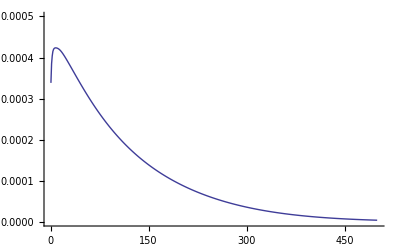

```mathematica
ListPlot[data1,Joined-> True,PlotRange-> {{0,500},{0,0.0005}}]
```

## C_ab-quantum

```mathematica
Te=100.;  (* keV *)
Ti=100.;  (* keV *)
ne=1.E25; (* cm^-3 *)
np=1.E25;(* cm^-3 *)
Ze=-1;
Zp=1;
Ze*ne + Zp*np;
c2=c^2;
```

```mathematica
f[eta_]:=Re[PolyGamma[1 + I*eta]-Log[eta]] 

Vei[te_,ti_]:=c √(te/mec2 +  ti/mpc2)
Etaei[te_,ti_] := (Be*Abs[Ze*Zp]*(2 a0 c))/(hbarc * Vei[te,ti])
dCeiScaled[x_,te_,ti_]:= Exp[-x/2]*f[Etaei[te,ti]/(√x)]
CeiScaled[te_,ti_]:= NIntegrate[dCeiScaled[x_,te,ti],{x,0,∞}]
```

1.32655×10^10

0.0164916

0.33984

7.17414

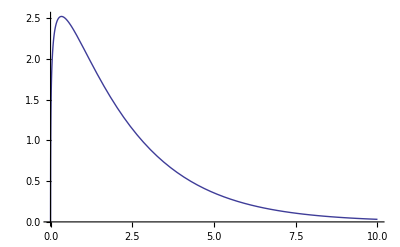

```mathematica
Vei[Te,Ti]
Etaei[Te,Ti]
x0=0.001;
dCeiScaled[x0, Te,Ti] 
a1=NIntegrate[dCeiScaled[x, Te,Ti],{x,0,Infinity}] 
gr1=Plot[dCeiScaled[x,Te,Ti],{x,0,10}]
```

```mathematica
st=OpenRead["dCeiQuantum1.0.dat"];
Do[Read[st,String],{i,1,21}]
ne=Read[st,Number]
Te=Read[st,Number]
Ti=Read[st,Number]
nn=Read[st,Number]
data=Table[Read[st,{Number,Number,Number}],{i,1,nn}];
dQM=Table[{data[[ix,2]],data[[ix,3]]},{ix,1,Length[data]}]
Close[st];
dQMint=Interpolation[dQM]
```

1.×10^25

100.

100.

500

{{0.,0.},{0.02,1.57255},{0.06,2.06391},{0.1,2.26393},{0.14,2.37509},{0.18,2.44243},{0.22,2.48366},{0.26,2.50762},{0.3,2.51941},{0.34,2.52221},{0.38,2.51817},{0.42,2.5088},{0.46,2.49521},{0.5,2.47823},{0.54,2.4585},{0.58,2.43652},{0.62,2.4127},{0.66,2.38738},{0.7,2.36082},{0.74,2.33324},{0.78,2.30485},{0.82,2.27579},{0.86,2.24621},{0.9,2.21621},{0.94,2.18591},{0.98,2.15538},{1.02,2.1247},{1.06,2.09395},{1.1,2.06316},{1.14,2.0324},{1.18,2.00171},{1.22,1.97113},{1.26,1.94068},{1.3,1.91041},{1.34,1.88033},{1.38,1.85047},{1.42,1.82085},{1.46,1.79148},{1.5,1.76239},{1.54,1.73358},{1.58,1.70507},{1.62,1.67687},{1.66,1.64898},{1.7,1.62141},{1.74,1.59418},{1.78,1.56728},{1.82,1.54071},{1.86,1.51449},{1.9,1.48862},{1.94,1.46309},{1.98,1.43791},{2.02,1.41307},{2.06,1.38859},{2.1,1.36446},{2.14,1.34068},{2.18,1.31724},{2.22,1.29415},{2.26,1.27141},{2.3,1.24901},{2.34,1.22696},{2.38,1.20524},{2.42,1.18386},{2.46,1.16281},{2.5,1.1421},{2.54,1.12171},{2.58,1.10165},{2.62,1.08191},{2.66,1.06249},{2.7,1.04338},{2.74,1.02459},{2.78,1.00611},{2.82,0.987929},{2.86,0.970052},{2.9,0.952472},{2.94,0.935186},{2.98,0.918191},{3.02,0.901482},{3.06,0.885056},{3.1,0.868908},{3.14,0.853036},{3.18,0.837435},{3.22,0.822102},{3.26,0.807033},{3.3,0.792223},{3.34,0.77767},{3.38,0.763369},{3.42,0.749317},{3.46,0.73551},{3.5,0.721945},{3.54,0.708617},{3.58,0.695523},{3.62,0.68266},{3.66,0.670023},{3.7,0.65761},{3.74,0.645417},{3.78,0.633441},{3.82,0.621677},{3.86,0.610123},{3.9,0.598775},{3.94,0.58763},{3.98,0.576684},{4.02,0.565935},{4.06,0.555379},{4.1,0.545012},{4.14,0.534833},{4.18,0.524837},{4.22,0.515022},{4.26,0.505384},{4.3,0.495921},{4.34,0.48663},{4.38,0.477507},{4.42,0.46855},{4.46,0.459757},{4.5,0.451123},{4.54,0.442648},{4.58,0.434327},{4.62,0.426158},{4.66,0.418139},{4.7,0.410267},{4.74,0.402539},{4.78,0.394953},{4.82,0.387507},{4.86,0.380197},{4.9,0.373022},{4.94,0.36598},{4.98,0.359067},{5.02,0.352282},{5.06,0.345623},{5.1,0.339086},{5.14,0.332671},{5.18,0.326374},{5.22,0.320194},{5.26,0.314129},{5.3,0.308177},{5.34,0.302335},{5.38,0.296601},{5.42,0.290975},{5.46,0.285453},{5.5,0.280034},{5.54,0.274716},{5.58,0.269497},{5.62,0.264375},{5.66,0.25935},{5.7,0.254418},{5.74,0.249578},{5.78,0.244829},{5.82,0.240169},{5.86,0.235596},{5.9,0.231109},{5.94,0.226706},{5.98,0.222386},{6.02,0.218147},{6.06,0.213987},{6.1,0.209906},{6.14,0.205901},{6.18,0.201971},{6.22,0.198116},{6.26,0.194333},{6.3,0.190622},{6.34,0.18698},{6.38,0.183407},{6.42,0.179901},{6.46,0.176462},{6.5,0.173087},{6.54,0.169777},{6.58,0.166528},{6.62,0.163341},{6.66,0.160215},{6.7,0.157147},{6.74,0.154138},{6.78,0.151186},{6.82,0.148289},{6.86,0.145448},{6.9,0.14266},{6.94,0.139925},{6.98,0.137242},{7.02,0.13461},{7.06,0.132027},{7.1,0.129494},{7.14,0.127009},{7.18,0.124571},{7.22,0.12218},{7.26,0.119834},{7.3,0.117532},{7.34,0.115274},{7.38,0.11306},{7.42,0.110887},{7.46,0.108756},{7.5,0.106665},{7.54,0.104614},{7.58,0.102603},{7.62,0.100629},{7.66,0.0986936},{7.7,0.0967948},{7.74,0.0949321},{7.78,0.093105},{7.82,0.0913128},{7.86,0.0895548},{7.9,0.0878304},{7.94,0.0861389},{7.98,0.0844797},{8.02,0.0828522},{8.06,0.0812558},{8.1,0.07969},{8.14,0.0781541},{8.18,0.0766475},{8.22,0.0751698},{8.26,0.0737204},{8.3,0.0722987},{8.34,0.0709042},{8.38,0.0695365},{8.42,0.0681949},{8.46,0.066879},{8.5,0.0655884},{8.54,0.0643225},{8.58,0.0630808},{8.62,0.061863},{8.66,0.0606685},{8.7,0.0594969},{8.74,0.0583478},{8.78,0.0572207},{8.82,0.0561153},{8.86,0.0550311},{8.9,0.0539677},{8.94,0.0529248},{8.98,0.0519018},{9.02,0.0508985},{9.06,0.0499145},{9.1,0.0489494},{9.14,0.0480029},{9.18,0.0470745},{9.22,0.046164},{9.26,0.045271},{9.3,0.0443952},{9.34,0.0435362},{9.38,0.0426938},{9.42,0.0418675},{9.46,0.0410572},{9.5,0.0402625},{9.54,0.039483},{9.58,0.0387186},{9.62,0.0379689},{9.66,0.0372336},{9.7,0.0365125},{9.74,0.0358053},{9.78,0.0351117},{9.82,0.0344315},{9.86,0.0337644},{9.9,0.0331102},{9.94,0.0324686},{9.98,0.0318393},{10.02,0.0312222},{10.06,0.030617},{10.1,0.0300234},{10.14,0.0294413},{10.18,0.0288705},{10.22,0.0283106},{10.26,0.0277616},{10.3,0.0272232},{10.34,0.0266951},{10.38,0.0261773},{10.42,0.0256695},{10.46,0.0251714},{10.5,0.024683},{10.54,0.024204},{10.58,0.0237343},{10.62,0.0232737},{10.66,0.0228219},{10.7,0.0223789},{10.74,0.0219444},{10.78,0.0215184},{10.82,0.0211006},{10.86,0.0206909},{10.9,0.020289},{10.94,0.019895},{10.98,0.0195086},{11.02,0.0191297},{11.06,0.018758},{11.1,0.0183936},{11.14,0.0180363},{11.18,0.0176858},{11.22,0.0173421},{11.26,0.0170051},{11.3,0.0166746},{11.34,0.0163506},{11.38,0.0160327},{11.42,0.0157211},{11.46,0.0154155},{11.5,0.0151158},{11.54,0.0148219},{11.58,0.0145337},{11.62,0.014251},{11.66,0.0139739},{11.7,0.0137021},{11.74,0.0134356},{11.78,0.0131743},{11.82,0.012918},{11.86,0.0126667},{11.9,0.0124203},{11.94,0.0121786},{11.98,0.0119417},{12.02,0.0117093},{12.06,0.0114814},{12.1,0.011258},{12.14,0.0110389},{12.18,0.010824},{12.22,0.0106133},{12.26,0.0104067},{12.3,0.0102041},{12.34,0.0100055},{12.38,0.00981067},{12.42,0.00961965},{12.46,0.00943233},{12.5,0.00924865},{12.54,0.00906854},{12.58,0.00889192},{12.62,0.00871874},{12.66,0.00854891},{12.7,0.00838239},{12.74,0.0082191},{12.78,0.00805898},{12.82,0.00790197},{12.86,0.00774801},{12.9,0.00759705},{12.94,0.00744901},{12.98,0.00730386},{13.02,0.00716152},{13.06,0.00702195},{13.1,0.00688509},{13.14,0.00675089},{13.18,0.00661931},{13.22,0.00649028},{13.26,0.00636375},{13.3,0.00623969},{13.34,0.00611804},{13.38,0.00599876},{13.42,0.00588179},{13.46,0.0057671},{13.5,0.00565464},{13.54,0.00554437},{13.58,0.00543625},{13.62,0.00533022},{13.66,0.00522626},{13.7,0.00512432},{13.74,0.00502437},{13.78,0.00492636},{13.82,0.00483026},{13.86,0.00473602},{13.9,0.00464363},{13.94,0.00455303},{13.98,0.00446419},{14.02,0.00437708},{14.06,0.00429167},{14.1,0.00420792},{14.14,0.0041258},{14.18,0.00404528},{14.22,0.00396633},{14.26,0.00388892},{14.3,0.00381301},{14.34,0.00373858},{14.38,0.00366561},{14.42,0.00359405},{14.46,0.00352388},{14.5,0.00345509},{14.54,0.00338763},{14.58,0.00332149},{14.62,0.00325664},{14.66,0.00319305},{14.7,0.00313069},{14.74,0.00306956},{14.78,0.00300961},{14.82,0.00295084},{14.86,0.00289321},{14.9,0.0028367},{14.94,0.00278129},{14.98,0.00272696},{15.02,0.0026737},{15.06,0.00262147},{15.1,0.00257026},{15.14,0.00252005},{15.18,0.00247081},{15.22,0.00242254},{15.26,0.00237521},{15.3,0.0023288},{15.34,0.00228329},{15.38,0.00223868},{15.42,0.00219493},{15.46,0.00215204},{15.5,0.00210998},{15.54,0.00206874},{15.58,0.00202831},{15.62,0.00198867},{15.66,0.0019498},{15.7,0.00191169},{15.74,0.00187432},{15.78,0.00183768},{15.82,0.00180176},{15.86,0.00176653},{15.9,0.001732},{15.94,0.00169814},{15.98,0.00166494},{16.02,0.00163238},{16.06,0.00160047},{16.1,0.00156917},{16.14,0.00153849},{16.18,0.0015084},{16.22,0.00147891},{16.26,0.00144998},{16.3,0.00142163},{16.34,0.00139382},{16.38,0.00136656},{16.42,0.00133983},{16.46,0.00131363},{16.5,0.00128793},{16.54,0.00126274},{16.58,0.00123804},{16.62,0.00121382},{16.66,0.00119008},{16.7,0.00116679},{16.74,0.00114397},{16.78,0.00112159},{16.82,0.00109964},{16.86,0.00107813},{16.9,0.00105703},{16.94,0.00103635},{16.98,0.00101607},{17.02,0.000996189},{17.06,0.000976695},{17.1,0.000957581},{17.14,0.000938842},{17.18,0.000920468},{17.22,0.000902453},{17.26,0.000884791},{17.3,0.000867474},{17.34,0.000850495},{17.38,0.000833848},{17.42,0.000817526},{17.46,0.000801523},{17.5,0.000785833},{17.54,0.00077045},{17.58,0.000755367},{17.62,0.00074058},{17.66,0.000726081},{17.7,0.000711866},{17.74,0.000697929},{17.78,0.000684264},{17.82,0.000670866},{17.86,0.000657731},{17.9,0.000644852},{17.94,0.000632225},{17.98,0.000619845},{18.02,0.000607707},{18.06,0.000595806},{18.1,0.000584138},{18.14,0.000572698},{18.18,0.000561482},{18.22,0.000550486},{18.26,0.000539704},{18.3,0.000529134},{18.34,0.00051877},{18.38,0.000508609},{18.42,0.000498646},{18.46,0.000488879},{18.5,0.000479302},{18.54,0.000469913},{18.58,0.000460708},{18.62,0.000451683},{18.66,0.000442834},{18.7,0.000434158},{18.74,0.000425652},{18.78,0.000417313},{18.82,0.000409137},{18.86,0.000401121},{18.9,0.000393261},{18.94,0.000385556},{18.98,0.000378001},{19.02,0.000370594},{19.06,0.000363332},{19.1,0.000356212},{19.14,0.000349232},{19.18,0.000342388},{19.22,0.000335678},{19.26,0.000329099},{19.3,0.00032265},{19.34,0.000316326},{19.38,0.000310126},{19.42,0.000304048},{19.46,0.000298089},{19.5,0.000292246},{19.54,0.000286518},{19.58,0.000280901},{19.62,0.000275395},{19.66,0.000269997},{19.7,0.000264704},{19.74,0.000259515},{19.78,0.000254428},{19.82,0.00024944},{19.86,0.00024455},{19.9,0.000239755},{19.94,0.000235055}}

InterpolatingFunction[{{0.,19.94}},<>]

{{0.1,1.86367×10^-21},{0.3,5.05897×10^-21},{0.5,7.62923×10^-21},{0.7,9.6645×10^-21},{0.9,1.12433×10^-20},{1.1,1.24341×10^-20},{1.3,1.32965×10^-20},{1.5,1.38821×10^-20},{1.7,1.42358×10^-20},{1.9,1.43966×10^-20},{2.1,1.43978×10^-20},{2.3,1.42684×10^-20},{2.5,1.40332×10^-20},{2.7,1.37136×10^-20},{2.9,1.33277×10^-20},{3.1,1.28911×10^-20},{3.3,1.24169×10^-20},{3.5,1.19162×10^-20},{3.7,1.13983×10^-20},{3.9,1.08711×10^-20},{4.1,1.03411×10^-20},{4.3,9.81341×10^-21},{4.5,9.29254×10^-21},{4.7,8.78194×10^-21},{4.9,8.28436×10^-21},{5.1,7.80196×10^-21},{5.3,7.33635×10^-21},{5.5,6.8887×10^-21},{5.7,6.45982×10^-21},{5.9,6.05017×10^-21},{6.1,5.66×10^-21},{6.3,5.28929×10^-21},{6.5,4.93788×10^-21},{6.7,4.60546×10^-21},{6.9,4.29159×10^-21},{7.1,3.99574×10^-21},{7.3,3.71734×10^-21},{7.5,3.45574×10^-21},{7.7,3.21027×10^-21},{7.9,2.98022×10^-21},{8.1,2.76488×10^-21},{8.3,2.56354×10^-21},{8.5,2.37548×10^-21},{8.7,2.2×10^-21},{8.9,2.03641×10^-21},{9.1,1.88402×10^-21},{9.3,1.7422×10^-21},{9.5,1.61031×10^-21},{9.7,1.48774×10^-21},{9.9,1.37392×10^-21},{10.1,1.26829×10^-21},{10.3,1.17032×10^-21},{10.5,1.07951×10^-21},{10.7,9.95389×10^-22},{10.9,9.175×10^-22},{11.1,8.45421×10^-22},{11.3,7.78752×10^-22},{11.5,7.17116×10^-22},{11.7,6.60158×10^-22},{11.9,6.07546×10^-22},{12.1,5.5897×10^-22},{12.3,5.14137×10^-22},{12.5,4.72775×10^-22},{12.7,4.34629×10^-22},{12.9,3.99461×10^-22},{13.1,3.67052×10^-22},{13.3,3.37193×10^-22},{13.5,3.09692×10^-22},{13.7,2.84373×10^-22},{13.9,2.61067×10^-22},{14.1,2.39623×10^-22},{14.3,2.19895×10^-22},{14.5,2.01752×10^-22},{14.7,1.85071×10^-22},{14.9,1.69737×10^-22},{15.1,1.55646×10^-22},{15.3,1.427×10^-22},{15.5,1.30808×10^-22},{15.7,1.19887×10^-22},{15.9,1.0986×10^-22},{16.1,1.00656×10^-22},{16.3,9.22088×10^-23},{16.5,8.44577×10^-23},{16.7,7.73468×10^-23},{16.9,7.08244×10^-23},{17.1,6.4843×10^-23},{17.3,5.93586×10^-23},{17.5,5.43308×10^-23},{17.7,4.97224×10^-23},{17.9,4.5499×10^-23},{18.1,4.16292×10^-23},{18.3,3.80839×10^-23},{18.5,3.48363×10^-23},{18.7,3.1862×10^-23},{18.9,2.91383×10^-23},{19.1,2.66444×10^-23},{19.3,2.43613×10^-23},{19.5,2.22714×10^-23},{19.7,2.03587×10^-23}}

7.1752

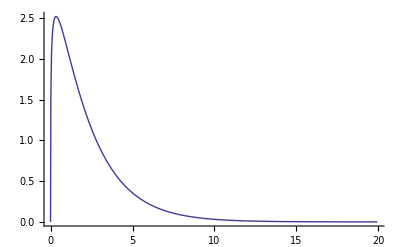

```mathematica
a2=NIntegrate[dQMint[x],{x,0,20}] 
gr2=ListPlot[dQM,Joined-> True]
```

{7.17414,7.1752}

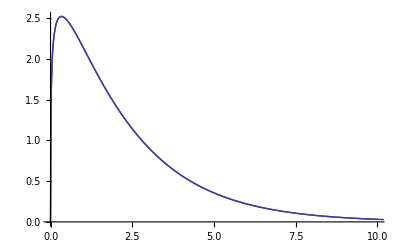

```mathematica
{a1,a2}
Show[gr1,gr2]
```

## C_ab-regular

```mathematica
Te=100.;  (* keV *)
Ti=100.;  (* keV *)
ne=1.E25; (* cm^-3 *)
np=1.E25;(* cm^-3 *)
Ze=-1;
Zp=1;
Ze*ne + Zp*np;
c2=c^2;
```

```mathematica
st=OpenRead["cei1.dat"];
Do[Read[st,String],{i,1,21}]
ne=Read[st,Number]
Te=Read[st,Number]
Ti=Read[st,Number]
nn=Read[st,Number]
data=Table[Read[st,{Number,Number,Number}],{i,1,nn}];
dQM=Table[{data[[ix,2]],data[[ix,3]]},{ix,1,Length[data]}]
Close[st];
dQMint=Interpolation[dQM]
```

1.×10^25

100.

100.

100

{{0.,0.},{0.050000000000000003,-0.0047582759257959514},{0.15,-0.04154909353949416},{0.25,-0.10863},{0.35,-0.194366},{0.45,-0.284414},{0.55,-0.364568},{0.65,-0.423494},{0.75,-0.454599},{0.85,-0.456779},{0.95,-0.433916},{1.05,-0.393328},{1.15,-0.343615},{1.25,-0.292508},{1.35,-0.245317},{1.45,-0.204426},{1.55,-0.169841},{1.65,-0.140373},{1.75,-0.114748},{1.85,-0.092178523148930824},{1.95,-0.072394734219443813},{2.05,-0.055408309793987594},{2.15,-0.041261221810535639},{2.25,-0.029881789239320673},{2.35,-0.021050170819525323},{2.45,-0.014431890599987458},{2.55,-0.0096361070959093322},{2.65,-0.0062703361629279685},{2.75,-0.0039789910618783821},{2.85,-0.0024637753492091742},{2.95,-0.0014893482982093391},{3.05,-0.00087932337315436851},{3.15,-0.00050724815878329117},{3.25,-0.00028598949771817814},{3.35,-0.00015763592718421614},{3.45,-0.000084964301435092268},{3.55,-0.000044789927754200308},{3.65,-0.00002309731232624925},{3.75,-0.000011653183999664294},{3.85,-5.7528966934808921×10^-6},{3.95,-2.7793122355249332×10^-6},{4.05,-1.314138703180484×10^-6},{4.15,-6.0818780721167383×10^-7},{4.25,-2.7552583802032558×10^-7},{4.35,-1.2219321695638533×10^-7},{4.45,-5.3054357587093979×10^-8},{4.55,-2.2553331074672492×10^-8},{4.65,-9.3872901225524191×10^-9},{4.75,-3.8258854880316806×10^-9},{4.85,-1.5268852998558498×10^-9},{4.95,-5.9673647154636943×10^-10},{5.05,-2.2849360708197755×10^-10},{5.15,-8.5644792543239534×10^-11},{5.25,-3.1439712753567773×10^-11},{5.35,-1.1303713900140158×10^-11},{5.45,-3.9805411609858004×10^-12},{5.55,-1.3729478477411898×10^-12},{5.65,-4.6384060116656631×10^-13},{5.75,-1.5349613124329624×10^-13},{5.85,-4.9756586824076088×10^-14},{5.95,-1.5799310715688712×10^-14},{6.05,-4.9143887411931963×10^-15},{6.15,-1.497454301657346×10^-15},{6.25,-4.469910019430084×10^-16},{6.35,-1.3071129355751074×10^-16},{6.45,-3.7445890760586119×10^-17},{6.55,-1.0509429894371572×10^-17},{6.65,-2.8896480604406337×10^-18},{6.75,-7.784094242364538×10^-19},{6.85,-2.0543516545381114×10^-19},{6.95,-5.3119134979306321×10^-20},{7.05,-1.3456817978162706×10^-20},{7.15,-3.3400606438231888×10^-21},{7.25,-8.1225443518278431×10^-22},{7.35,-1.9353545832594934×10^-22},{7.45,-4.5181895919590897×10^-23},{7.55,-1.0334949158541221×10^-23},{7.65,-2.3163094219259989×10^-24},{7.75,-5.086666994467155×10^-25},{7.85,-1.0945170800742896×10^-25},{7.95,-2.307640336405713×10^-26},{8.05,-4.7673136885206633×10^-27},{8.15,-9.6503465578888582×10^-28},{8.25,-1.9141636708178285×10^-28},{8.35,-3.7203644458328271×10^-29},{8.45,-7.0854153050180943×10^-30},{8.55,-1.3222743796268599×10^-30},{8.65,-2.4180051763286897×10^-31},{8.75,-4.3328640132799306×10^-32},{8.85,-7.6081277874000016×10^-33},{8.95,-1.3090856599466393×10^-33},{9.05,-2.2072340570710727×10^-34},{9.15,-3.6468777750520325×10^-35},{9.25,-5.904578228554874×10^-36},{9.35,-9.3681466950522757×10^-37},{9.45,-1.4565245630388615×10^-37},{9.55,-2.2191333367217264×10^-38},{9.65,-3.3132369176932783×10^-39},{9.75,-4.8476034244527796×10^-40},{9.85,-6.950388748451225×10^-41}}

InterpolatingFunction[{{0.,9.85}},<>]

{{0.1,1.86367×10^-21},{0.3,5.05897×10^-21},{0.5,7.62923×10^-21},{0.7,9.6645×10^-21},{0.9,1.12433×10^-20},{1.1,1.24341×10^-20},{1.3,1.32965×10^-20},{1.5,1.38821×10^-20},{1.7,1.42358×10^-20},{1.9,1.43966×10^-20},{2.1,1.43978×10^-20},{2.3,1.42684×10^-20},{2.5,1.40332×10^-20},{2.7,1.37136×10^-20},{2.9,1.33277×10^-20},{3.1,1.28911×10^-20},{3.3,1.24169×10^-20},{3.5,1.19162×10^-20},{3.7,1.13983×10^-20},{3.9,1.08711×10^-20},{4.1,1.03411×10^-20},{4.3,9.81341×10^-21},{4.5,9.29254×10^-21},{4.7,8.78194×10^-21},{4.9,8.28436×10^-21},{5.1,7.80196×10^-21},{5.3,7.33635×10^-21},{5.5,6.8887×10^-21},{5.7,6.45982×10^-21},{5.9,6.05017×10^-21},{6.1,5.66×10^-21},{6.3,5.28929×10^-21},{6.5,4.93788×10^-21},{6.7,4.60546×10^-21},{6.9,4.29159×10^-21},{7.1,3.99574×10^-21},{7.3,3.71734×10^-21},{7.5,3.45574×10^-21},{7.7,3.21027×10^-21},{7.9,2.98022×10^-21},{8.1,2.76488×10^-21},{8.3,2.56354×10^-21},{8.5,2.37548×10^-21},{8.7,2.2×10^-21},{8.9,2.03641×10^-21},{9.1,1.88402×10^-21},{9.3,1.7422×10^-21},{9.5,1.61031×10^-21},{9.7,1.48774×10^-21},{9.9,1.37392×10^-21},{10.1,1.26829×10^-21},{10.3,1.17032×10^-21},{10.5,1.07951×10^-21},{10.7,9.95389×10^-22},{10.9,9.175×10^-22},{11.1,8.45421×10^-22},{11.3,7.78752×10^-22},{11.5,7.17116×10^-22},{11.7,6.60158×10^-22},{11.9,6.07546×10^-22},{12.1,5.5897×10^-22},{12.3,5.14137×10^-22},{12.5,4.72775×10^-22},{12.7,4.34629×10^-22},{12.9,3.99461×10^-22},{13.1,3.67052×10^-22},{13.3,3.37193×10^-22},{13.5,3.09692×10^-22},{13.7,2.84373×10^-22},{13.9,2.61067×10^-22},{14.1,2.39623×10^-22},{14.3,2.19895×10^-22},{14.5,2.01752×10^-22},{14.7,1.85071×10^-22},{14.9,1.69737×10^-22},{15.1,1.55646×10^-22},{15.3,1.427×10^-22},{15.5,1.30808×10^-22},{15.7,1.19887×10^-22},{15.9,1.0986×10^-22},{16.1,1.00656×10^-22},{16.3,9.22088×10^-23},{16.5,8.44577×10^-23},{16.7,7.73468×10^-23},{16.9,7.08244×10^-23},{17.1,6.4843×10^-23},{17.3,5.93586×10^-23},{17.5,5.43308×10^-23},{17.7,4.97224×10^-23},{17.9,4.5499×10^-23},{18.1,4.16292×10^-23},{18.3,3.80839×10^-23},{18.5,3.48363×10^-23},{18.7,3.1862×10^-23},{18.9,2.91383×10^-23},{19.1,2.66444×10^-23},{19.3,2.43613×10^-23},{19.5,2.22714×10^-23},{19.7,2.03587×10^-23}}

-0.502368

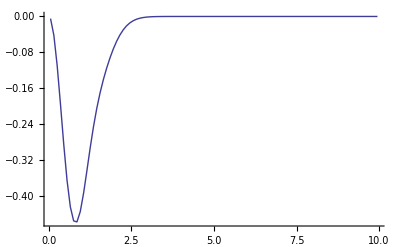

```mathematica
a1=NIntegrate[dQMint[x],{x,0,10}] 
gr1=ListPlot[dQM,Joined-> True,PlotRange-> All]
```

```mathematica
Te=10.;  (* keV *)
Ti=10.;  (* keV *)
ne=1.E25; (* cm^-3 *)
np=1.E25;(* cm^-3 *)
Ze=-1;
Zp=1;
Ze*ne + Zp*np;
c2=c^2;
```

```mathematica
st=OpenRead["cei.dat"];
Do[Read[st,String],{i,1,21}]
nn=100;
data=Table[Read[st,{Number,Number,Number}],{i,1,nn}];
Clear[dQM,dQMint]
dQM=Table[{data[[ix,2]],data[[ix,3]]},{ix,1,Length[data]}]
Close[st];
dQMint=Interpolation[dQM]
```

{{0.050000000000000003,-0.0047582759257959514},{0.15,-0.04154909353949416},{0.25,-0.10863},{0.35,-0.194366},{0.45,-0.284414},{0.55,-0.364568},{0.65,-0.423494},{0.75,-0.454599},{0.85,-0.456779},{0.95,-0.433916},{1.05,-0.393328},{1.15,-0.343615},{1.25,-0.292508},{1.35,-0.245317},{1.45,-0.204426},{1.55,-0.169841},{1.65,-0.140373},{1.75,-0.114748},{1.85,-0.092178523148930824},{1.95,-0.072394734219443813},{2.05,-0.055408309793987594},{2.15,-0.041261221810535639},{2.25,-0.029881789239320673},{2.35,-0.021050170819525323},{2.45,-0.014431890599987458},{2.55,-0.0096361070959093322},{2.65,-0.0062703361629279685},{2.75,-0.0039789910618783821},{2.85,-0.0024637753492091742},{2.95,-0.0014893482982093391},{3.05,-0.00087932337315436851},{3.15,-0.00050724815878329117},{3.25,-0.00028598949771817814},{3.35,-0.00015763592718421614},{3.45,-0.000084964301435092268},{3.55,-0.000044789927754200308},{3.65,-0.00002309731232624925},{3.75,-0.000011653183999664294},{3.85,-5.7528966934808921×10^-6},{3.95,-2.7793122355249332×10^-6},{4.05,-1.314138703180484×10^-6},{4.15,-6.0818780721167383×10^-7},{4.25,-2.7552583802032558×10^-7},{4.35,-1.2219321695638533×10^-7},{4.45,-5.3054357587093979×10^-8},{4.55,-2.2553331074672492×10^-8},{4.65,-9.3872901225524191×10^-9},{4.75,-3.8258854880316806×10^-9},{4.85,-1.5268852998558498×10^-9},{4.95,-5.9673647154636943×10^-10},{5.05,-2.2849360708197755×10^-10},{5.15,-8.5644792543239534×10^-11},{5.25,-3.1439712753567773×10^-11},{5.35,-1.1303713900140158×10^-11},{5.45,-3.9805411609858004×10^-12},{5.55,-1.3729478477411898×10^-12},{5.65,-4.6384060116656631×10^-13},{5.75,-1.5349613124329624×10^-13},{5.85,-4.9756586824076088×10^-14},{5.95,-1.5799310715688712×10^-14},{6.05,-4.9143887411931971×10^-15},{6.15,-1.497454301657346×10^-15},{6.25,-4.469910019430084×10^-16},{6.35,-1.3071129355751074×10^-16},{6.45,-3.7445890760586119×10^-17},{6.55,-1.0509429894371572×10^-17},{6.65,-2.8896480604406337×10^-18},{6.75,-7.784094242364538×10^-19},{6.85,-2.0543516545381114×10^-19},{6.95,-5.3119134979306321×10^-20},{7.05,-1.3456817978162706×10^-20},{7.15,-3.3400606438231888×10^-21},{7.25,-8.1225443518278431×10^-22},{7.35,-1.9353545832594934×10^-22},{7.45,-4.5181895919590897×10^-23},{7.55,-1.0334949158541221×10^-23},{7.65,-2.3163094219259989×10^-24},{7.75,-5.086666994467155×10^-25},{7.85,-1.0945170800742896×10^-25},{7.95,-2.307640336405713×10^-26},{8.05,-4.7673136885206633×10^-27},{8.15,-9.6503465578888582×10^-28},{8.25,-1.9141636708178285×10^-28},{8.35,-3.7203644458328271×10^-29},{8.45,-7.0854153050180943×10^-30},{8.55,-1.3222743796268599×10^-30},{8.65,-2.4180051763286897×10^-31},{8.75,-4.3328640132799306×10^-32},{8.85,-7.6081277874000016×10^-33},{8.95,-1.3090856599466393×10^-33},{9.05,-2.2072340570710727×10^-34},{9.15,-3.6468777750520325×10^-35},{9.25,-5.904578228554874×10^-36},{9.35,-9.3681466950522757×10^-37},{9.45,-1.4565245630388615×10^-37},{9.55,-2.2191333367217264×10^-38},{9.65,-3.3132369176932783×10^-39},{9.75,-4.8476034244527796×10^-40},{9.85,-6.950388748451225×10^-41},{9.95,-9.765632814426339×10^-42}}

InterpolatingFunction[{{0.05,9.95}},<>]

```mathematica
a2=NIntegrate[dQMint[x],{x,0,10}] 
gr2=ListPlot[dQM,Joined-> True,PlotRange-> All]
```

-0.502368

-Graphics-